# NG^21 P_02. Наивный байесовский классификатор

Бельская Екатерина, 5 группа, 2 курс

## Задание 1. Гистограмма

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
ClearAll[LoadMNIST];
LoadMNIST[SetName_String]:=Module[{F,FDummy,Counter,Rows,Cols,Digits,Images},
F=OpenRead[ToLowerCase[SetName]<>"-images.idx3-ubyte",BinaryFormat->True];
{FDummy,Counter,Rows,Cols}=BinaryRead[F,Array["Integer32"&,4],ByteOrdering->+1];
Images=Fold[Partition[#,#2]&,BinaryReadList[F,"Byte",ByteOrdering->+1],{Cols,Rows}];
Close[F];
F=OpenRead[ToLowerCase[SetName]<>"-labels.idx1-ubyte",BinaryFormat->True];
{FDummy,Counter}=BinaryRead[F,Array["Integer32"&,2],ByteOrdering->+1];
Digits=BinaryReadList[F,"Byte",ByteOrdering->+1];
Close[F];
{Digits,Images}]
```

```mathematica
Map[Dimensions,Train=LoadMNIST["train"]]
```

{{60000},{60000,28,28}}

```mathematica
Map[Dimensions,Test=LoadMNIST["t10k"]]
```

{{10000},{10000,28,28}}

```mathematica
DynamicModule[{m=7},Grid[{
{Row@{"Magnification: ",SetterBar[Dynamic@m,Range[10]]},SpanFromLeft},{
Manipulate[Style[Train⟦1,n⟧,Bold,24+2m]->Image[256-Train⟦2,n⟧,"Byte",ColorSpace->"GrayScale",Magnification->m],{{n,37267,"Train"},1,Length@Train⟦1⟧,1,Appearance->"Labeled"},Paneled->False],
Manipulate[Style[Test⟦1,n⟧,Bold,24+2m]->Image[256-Test⟦2,n⟧,"Byte",ColorSpace->"GrayScale",Magnification->m],{{n,4655,"Test"},1,Length@Test⟦1⟧,1,Appearance->"Labeled"},Paneled->False]}},Frame->All,FrameStyle->Gray]]
```

```mathematica
digit=0;
row=13;
col=17;
```

Список позиций моей цифры

```mathematica
friendTrain=Flatten@Position[Train⟦1⟧,digit];
```

Список позиций всех оставшихся цифр

```mathematica
foeTrain=Complement[Range[Length@Train⟦1⟧], friendTrain];
```

Фиксированный пиксель

```mathematica
trainPixelFriend=Train⟦2,friendTrain,row, col⟧;
```

```mathematica
trainPixelFoe=Train⟦2,foeTrain,row, col⟧;
```

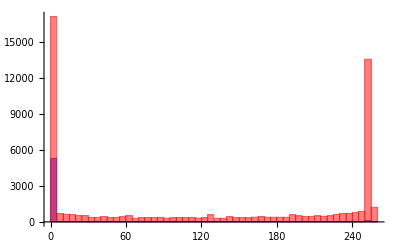

```mathematica
Histogram[{trainPixelFriend, trainPixelFoe},50,ChartStyle->{Blue, Red}]
```

Пиксели растров класса "Свой", находящихся в данной строке и данном столбце имеют в большинстве случаев близкое к 0 числовое значение. Пиксели растров класса "Чужов", располагающихся в этом столбце и этой строке имеют преимущественно нулевое числовое значение или значение, равное ~250. Это означает, что начертание цифры 0 практически во всех случаях "не затрагивает" или “затрагивает мало” пиксель на  пересечении исходной строки и исходного столбца, в отличие от остальных цифр.

## Задание 2. Нормально распределенная случайная величина

Сумма всех пикселей, попадающих в данный столбец для friendTrain и foeTrain

```mathematica
trainFriendCols=Total[Train⟦2,friendTrain,;;, col⟧,{2}];
trainFoeCols=Total[Train⟦2,foeTrain,;;, col⟧,{2}];
```

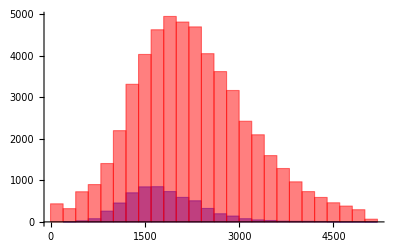

```mathematica
Histogram[{trainFriendCols, trainFoeCols}, Automatic, ChartStyle->{Blue, Red}]
```

Сумма всех пикселей, попадающих в данную строку для friendTrain и foeTrain

```mathematica
trainFriendRows=Total[Train⟦2,friendTrain,row, ;;⟧,{2}];
trainFoeRows=Total[Train⟦2,foeTrain,row, ;;⟧,{2}];
```

```mathematica
Histogram[{trainFriendRows, trainFoeRows}, ChartStyle->{Blue, Red}]
```

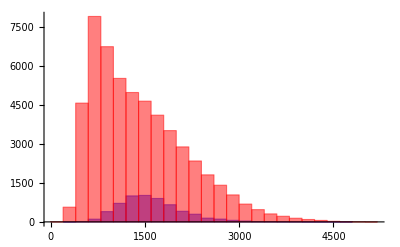

Сумма всех пикселей, попадающих в данную строку и данный столбец для friendTrain и foeTrain

```mathematica
trainFriendCross=trainFriendCols+trainFriendRows-trainPixelFriend;
trainFoeCross=trainFoeCols+trainFoeRows-trainPixelFoe;
```

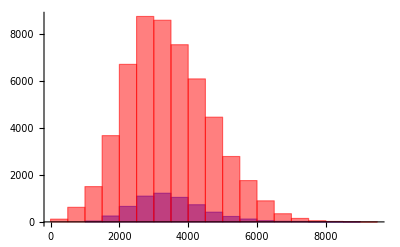

```mathematica
Histogram[{trainFriendCross, trainFoeCross},ChartStyle->{Blue, Red}]
```

Сравнение с граничным пикселем (находится под исходным)

Фиксированный пиксель

```mathematica
btrainPixelFriend=Train⟦2,friendTrain,row+1, col⟧;
btrainPixelFoe=Train⟦2,foeTrain,row+1, col⟧;
```

```mathematica
PairedHistogram[{trainPixelFriend, trainPixelFoe},{btrainPixelFriend, btrainPixelFoe},ChartStyle->{Blue, Red}]
```

-Graphics-

Сумма всех пикселей, попадающих в данную строку для friendTrain и foeTrain

```mathematica
btrainFriendRows=Total[Train⟦2,friendTrain,row+1, ;;⟧,{2}];
btrainFoeRows=Total[Train⟦2,foeTrain,row+1, ;;⟧,{2}];
```

```mathematica
PairedHistogram[{trainFriendRows,trainFoeRows},{btrainFriendRows, btrainFoeRows}, ChartStyle->{Blue, Red}]
```

-Graphics-

Сумма всех пикселей, попадающих в данную строку и данный столбец для friendTrain и foeTrain (значения сумм всех пикселей, попадающих в фиксированный столбец совпадают с исходными)

```mathematica
btrainFriendCross=trainFriendCols+btrainFriendRows-btrainPixelFriend;
btrainFoeCross=trainFoeCols+btrainFoeRows-btrainPixelFoe;
```

```mathematica
PairedHistogram[{trainFriendCross,trainFoeCross},{btrainFriendCross, btrainFoeCross}, ChartStyle->{Blue, Red}]
```

-Graphics-

Гистограммы для исходного и граничного пикселя показывают, что числовые значения пикселей и других числовых характеристик соответственно (скан-строка, скан-столбец, скан-крест) практически одинаковы. Это значит, что с большего начертание цифры проходит как через исходный пиксель, так и через его “соседа”

## Задание 3. Функция плотности вероятности

Функции нахождения среднего значения и стандартного отклонения

```mathematica
ClearAll[μfind];
μfind[l_]:=Mean[l]//N;
```

```mathematica
ClearAll[σfind];
σfind[l_]:=StandardDeviation[l]//N;
```

Нахождение среднего значения и стандартного отклонения для каждого из четырёх параметров : пиксель, скан - строка, скан - столбец и скан - крест, —для объектов "Свой" и "Чужой"

```mathematica
fr={μfind[#],σfind[#]}&/@{trainPixelFriend,trainFriendRows,trainFriendCols,trainFriendCross}
```

{{13.8749,49.0929},{1681.9,561.632},{1814.05,605.934},{3482.07,1028.85}}

```mathematica
foe={μfind[#],σfind[#]}&/@{trainPixelFoe,trainFoeRows,trainFoeCols,trainFoeCross}
```

{{123.899,109.216},{1301.69,674.764},{2254.91,929.461},{3432.7,1230.64}}

Список из графиков функций плотности вероятности для нормальной распределенной случайной величины, наложенных на соотвествующие гистограммы плотности вероятности

```mathematica
grlist=MapThread[Show[Histogram[#1, 50,  "PDF",ChartStyle->{Blue, Red}], Plot[PDF[NormalDistribution[#2⟦1⟧,#2⟦2⟧],x],{x,#2⟦1⟧-3*#2⟦2⟧, #2⟦1⟧+3*#2⟦2⟧},PlotStyle->Blue,Filling->Axis], Plot[PDF[NormalDistribution[#3⟦1⟧,#3⟦2⟧],x],{x,#3⟦1⟧-3*#3⟦2⟧, #3⟦1⟧+3*#3⟦2⟧},PlotStyle->Red,Filling->Axis]]&,{{{trainPixelFriend,trainPixelFoe},{trainFriendRows, trainFoeRows},{trainFriendCols, trainFoeCols},{trainFriendCross, trainFoeCross}},fr,foe}];
```

```mathematica
Manipulate[grlist[[t]],{{t,1,"For:"},{1->"Pixel",2->"Rows",3->"Cols",4->"Cross"}}]
```

Полученные выше гистограммы плотности вероятности достаточно близки по значениям к значениям функции плотности вероятности для определенных величин (trainPixelFriend, trainPixelFoe и так далее)

## Задание 4.

row, col - соответственно номер строки и столбца, l - набор растров в Train или Test, ll - сам исходный Train или Test

```mathematica
ClearAll[Feature];
Feature[row_Integer,l_,ll_]:=Total[ll⟦2,l,row, ;;⟧,{2}];
Feature[l_,col_Integer,ll_]:=Total[ll⟦2,l,;;, col⟧,{2}];
Feature[l_,ll_]:={Feature[#,l,ll],Feature[l,#,ll]}&/@Range[28];
```

Вычисление всех скан - строк и всех скан - столбцов для всех растров в тренировочном наборе Train. ltrain - список, состоящий 28 подсписков, каждый из которых состоит из 2 списков : скан - строк и скан - столбцов (номер строки = номер столбца) для всех растров

```mathematica
ltrain=Feature[Range[Length@Train⟦1⟧],Train]
```

{1}
 |  |  |  |

Функция нахождения среднего значения и стандартного отклонения. Входные параметры : список растров (будут использоваться friendTrain и foeTrain), i - число (1 или 2), определяющее списки для строк или списки для столбцов

```mathematica
ClearAll[μσ];
μσ[l_,i_]:=N@{Mean[#], StandardDeviation[#]}&/@(ltrain⟦#,i,l⟧&/@Range[28])
```

Вычисление для каждого параметра среднего значения и стандартного отклонения объектов "свой" и "чужой"

```mathematica
frrows=μσ[friendTrain,1];
```

```mathematica
frcols=μσ[friendTrain,2];
```

```mathematica
foerows=μσ[foeTrain,1];
```

```mathematica
foecols=μσ[foeTrain,2];
```

Функция вычисления весовых коэффициентов

```mathematica
ClearAll[wcount];
wcount[{l1_,l2_}]:=MapThread[If[#1⟦2⟧*#2⟦2⟧==0,0,(#1⟦1⟧-#2⟦1⟧)/(#1⟦2⟧*#2⟦2⟧)]&,{l1,l2}];
```

Список весовых коэффициентов для параметров - строк

```mathematica
wrows=wcount[{frrows,foerows}]
```

{0,-0.00711139,-0.0256023,-0.00195794,0.000412269,0.00082104,0.00103801,0.00122059,0.00116708,0.00113903,0.0012694,0.00134107,0.00100328,0.000480129,0.000132069,0.0000931971,0.000345606,0.000729494,0.000950919,0.001085,0.00137574,0.00171602,0.0014242,0.00063727,-0.000727183,-0.0110902,0,0}

Список весовых коэффициентов для параметров - столбцов

```mathematica
wcols=wcount[{frcols,foecols}]
```

{-0.0127498,-0.0119816,-0.0231935,-0.00424499,0.00101484,0.00168659,0.00170653,0.00181814,0.00187356,0.00151132,0.000898763,0.000361935,-0.000116094,-0.000620673,-0.000917159,-0.00105091,-0.00078279,-0.00024176,0.000383093,0.00112871,0.0018336,0.00211364,0.00217671,0.00221941,0.00174093,-0.00209093,-0.00793456,-0.00614457}

При разбросе показаний практически равным 0, получаем, что знаменатель дроби будет равен 0, поэтому полагаем, что весовой коэффициент такого параметра равен 0.

## Задание 5. Наивный байесовский классификатор

Функция - классификатор. Входные параметры : растр, список параметров для этого растра

```mathematica
ClearAll[NBC,w0];NBC[x_,l_]:=w0+wrows.(l⟦#,1,x⟧&/@Range[28])+wcols.(l⟦#,2,x⟧&/@Range[28])
```

Нахождение коэффициента w0

```mathematica
w0=w0/.Solve[Mean[NBC[foeTrain,ltrain]]==0,w0]
```

{-24.8994}

## Задание 6. Ошибки 1 - го и 2 - го рода

Вычисление всех скан - строк и всех скан - столбцов для всех растров в тренировочном наборе Test. ltest - список, состоящий 28 подсписков, каждый из которых состоит из 2 списков : скан - строк и скан - столбцов (номер строки = номер столбца) для всех растров

```mathematica
ltest=Feature[Range[Length@Test⟦1⟧],Test];
```

Список позиций моей цифры в наборе Test

```mathematica
friendTest=Flatten@Position[Test⟦1⟧,digit];
```

Список позиций всех оставшихся цифр наборе Test

```mathematica
foeTest=Complement[Range[Length@Test⟦1⟧], friendTest];
```

Функции, вычисляющая количество и процент ошибок. Входные параметры : список параметров для растра, сам растр, числовой параметр - 1 или 0 для вычисления соответсвтенно ошибок 1 - го и 2 - го рода

```mathematica
ClearAll[mistakesCount];
mistakesCount[l1_,l2_,i:(_1|_0)]:=Count[Flatten[UnitStep[NBC[#,l1]]&/@l2],i]
```

```mathematica
ClearAll[prCount];
prCount[l1_,l2_,i:(_1|_0)]:=N[mistakesCount[l1,l2,i]*100/Length[l2]]
```

Количество и процент ошибок первого рода

```mathematica
mistakesCount[ltest,friendTest,0]
```

19

```mathematica
prCount[ltest,friendTest,0]
```

1.93878

Количество и процент ошибок второго рода

```mathematica
mistakesCount[ltest,foeTest,1]
```

4178

```mathematica
prCount[ltest,foeTest,1]
```

46.3193

Результаты говорят о том, что процент ошибок первого рода достаточно мал, в то время как процент ошибок второго рода составляет практически 50 %